## Tau Soma Simulation Data Parser

```mathematica
h[Vin_]:=(π+2ArcCot[√(-1+2Vin)])/(√(-1+2Vin))
```

### Function Definitions

#### GetData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
GetData[fileName_]:=Module[{tauVals,iInVals,data,i},
i=Import[fileName,"Data"];
tauVals=Rest[i⟦1⟧];
iInVals =Rest[i⟦;;,1⟧];
data=i⟦2;;,2;;⟧;
Clear[i];
Return[{tauVals,iInVals, data}];
](* GetData Module *)
```

### Ask user to select an input file with the τ data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/SomaTauMeas", WindowTitle->"Select Parsed Simulation Data File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/SomaTauMeas

File Name: SomaSimTauData.txt

```mathematica
{tauVals, iInVals, data}=GetData[fileName];
(*i=Import[fileName,"Data"];
tauVals=Rest[i⟦1⟧];
iInVals =Rest[i⟦;;,1⟧];
data=i⟦2;;,2;;⟧;*)
Ilkbase=332.698*10^-15;
IlkValues={Ilkbase/0.1,Ilkbase/0.2,Ilkbase/0.5,Ilkbase/1.0,Ilkbase/1.5,Ilkbase/2.0,Ilkbase/2.5};
Print[Style["τ values: ", FontFamily->"Helvetica", Bold],tauVals];
Print[Style["I_lk values(A): (assuming Ilk= ", FontFamily->"Helvetica", Bold],
Ilkbase,
Style[" when τ=0.01s)", FontFamily->"Helvetica", Bold],
IlkValues];
Print[Style["ι_in values: ", FontFamily->"Helvetica", Bold],iInVals];
Print[Style["Raw Data Firing Rates: ", FontFamily->"Helvetica", Bold],data];
xValues=Transpose[h[#]&/@iInVals/#&/@IlkValues];
firingRatePlotVals=1/data;
plotVals=Transpose[{Take[xValues⟦#⟧,Length[firingRatePlotVals⟦#⟧]],firingRatePlotVals⟦#⟧}]&/@Range[Length[xValues]];
Print[Style["Plot Data: ", FontFamily->"Helvetica", Bold],plotVals];
```

τ values: {0.001,0.002,0.005,0.01,0.015,0.02,0.025}

I_lk values(A): (assuming Ilk= 3.32698×10^-13 when τ=0.01s){3.32698×10^-12,1.66349×10^-12,6.65396×10^-13,3.32698×10^-13,2.21799×10^-13,1.66349×10^-13,1.33079×10^-13}

ι_in values: {0.51,0.6,1,5,10,15,20,25,30,40,50,55,75,100,200,400}

Raw Data Firing Rates: {{47.716,23.221,8.0383,2.5097},{75.288,37.53,14.275,6.3187,3.5438,2.0769,1.045},{153.54,77.734,31.09,15.135,9.7605,7.0543,5.4028},{472.31,241.17,98.636,49.809,33.265,24.922,19.886},{675.19,344.83,141.24,71.612,47.996,36.087,28.892},{821.04,418.32,171.29,86.912,58.271,43.899,35.195},{938.42,477.74,195.33,99.108,66.59,50.121,40.199},{1039.2,527.77,215.55,109.4,73.457,55.333,44.414},{1127.3,571.5,233.29,118.38,79.498,59.941,48.092},{1279.6,646.88,263.42,133.57,89.767,67.683,54.329},{1410.8,711.32,288.91,146.34,98.359,74.16,59.553},{1470.5,740.52,300.49,152.08,102.17,77.009,61.855},{1680.9,842.55,340.33,172.05,115.54,87.074,69.948},{1902.3,948.39,381.41,192.51,129.18,97.315,78.196},{2574.2,1264.2,500.92,251.58,168.35,126.57,101.64},{3586.2,1728.7,670.87,331.87,221.,165.95,132.88}}

Plot Data: {(1.27569×10^13 | 0.0209573
2.55138×10^13 | 0.0430645
6.37846×10^13 | 0.124404
1.27569×10^14 | 0.398454),(3.65765×10^12 | 0.0132823
7.31531×10^12 | 0.0266454
1.82883×10^13 | 0.0700525
3.65765×10^13 | 0.15826
5.48648×10^13 | 0.282183
7.31531×10^13 | 0.481487
9.14414×10^13 | 0.956938),(1.41642×10^12 | 0.00651296
2.83283×10^12 | 0.0128644
7.08208×10^12 | 0.0321647
1.41642×10^13 | 0.066072
2.12462×10^13 | 0.102454
2.83283×10^13 | 0.141758
3.54104×10^13 | 0.185089),(3.79232×10^11 | 0.00211725
7.58464×10^11 | 0.00414645
1.89616×10^12 | 0.0101383
3.79232×10^12 | 0.0200767
5.68848×10^12 | 0.0300616
7.58464×10^12 | 0.0401252
9.4808×10^12 | 0.0502866),(2.47733×10^11 | 0.00148106
4.95466×10^11 | 0.00289998
1.23867×10^12 | 0.00708015
2.47733×10^12 | 0.0139641
3.716×10^12 | 0.0208351
4.95466×10^12 | 0.0277108
6.19333×10^12 | 0.0346117),(1.95844×10^11 | 0.00121797
3.91687×10^11 | 0.00239051
9.79218×10^11 | 0.00583805
1.95844×10^12 | 0.0115059
2.93765×10^12 | 0.0171612
3.91687×10^12 | 0.0227796
4.89609×10^12 | 0.0284131),(1.6649×10^11 | 0.00106562
3.32979×10^11 | 0.00209319
8.32448×10^11 | 0.00511954
1.6649×10^12 | 0.01009
2.49735×10^12 | 0.0150173
3.32979×10^12 | 0.0199517
4.16224×10^12 | 0.0248762),(1.47083×10^11 | 0.000962279
2.94165×10^11 | 0.00189476
7.35413×10^11 | 0.00463929
1.47083×10^12 | 0.00914077
2.20624×10^12 | 0.0136134
2.94165×10^12 | 0.0180724
3.67707×10^12 | 0.0225154),(1.33066×10^11 | 0.000887075
2.66133×10^11 | 0.00174978
6.65332×10^11 | 0.00428651
1.33066×10^12 | 0.00844737
1.996×10^12 | 0.0125789
2.66133×10^12 | 0.0166831
3.32666×10^12 | 0.0207935),(1.13817×10^11 | 0.000781494
2.27634×10^11 | 0.00154588
5.69086×10^11 | 0.00379622
1.13817×10^12 | 0.00748671
1.70726×10^12 | 0.01114
2.27634×10^12 | 0.0147748
2.84543×10^12 | 0.0184064),(1.00955×10^11 | 0.000708818
2.01911×10^11 | 0.00140584
5.04777×10^11 | 0.00346129
1.00955×10^12 | 0.0068334
1.51433×10^12 | 0.0101668
2.01911×10^12 | 0.0134844
2.52388×10^12 | 0.0167918),(9.59437×10^10 | 0.000680041
1.91887×10^11 | 0.0013504
4.79719×10^11 | 0.0033279
9.59437×10^11 | 0.00657549
1.43916×10^12 | 0.00978761
1.91887×10^12 | 0.0129855
2.39859×10^12 | 0.0161668),(8.13838×10^10 | 0.000594919
1.62768×10^11 | 0.00118687
4.06919×10^11 | 0.00293832
8.13838×10^11 | 0.00581226
1.22076×10^12 | 0.00865501
1.62768×10^12 | 0.0114845
2.03459×10^12 | 0.0142963),(6.99539×10^10 | 0.000525679
1.39908×10^11 | 0.00105442
3.49769×10^11 | 0.00262185
6.99539×10^11 | 0.00519454
1.04931×10^12 | 0.00774114
1.39908×10^12 | 0.0102759
1.74885×10^12 | 0.0127884),(4.87784×10^10 | 0.00038847
9.75568×10^10 | 0.000791014
2.43892×10^11 | 0.00199633
4.87784×10^11 | 0.00397488
7.31676×10^11 | 0.00594001
9.75568×10^11 | 0.00790077
1.21946×10^12 | 0.00983865),(3.41582×10^10 | 0.000278847
6.83164×10^10 | 0.000578469
1.70791×10^11 | 0.0014906
3.41582×10^11 | 0.00301323
5.12373×10^11 | 0.00452489
6.83164×10^11 | 0.00602591
8.53955×10^11 | 0.00752559)}

### Fit Data to a Linear Model

```mathematica
fitLineEq=Fit[#,{1,t},t]&/@plotVals
fitLineRules=FindFit[#,m t+b,{m,b},t]&/@plotVals;
```

plotVals

### Plot Data

```mathematica
Clear[currPlotNum];
Manipulate[
imageSize=500;
currPlotNum=Flatten[Position[iInVals,curriIn]]⟦1⟧;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[fitLineEq⟦currPlotNum⟧,Italic]}]},
{Show[
ListLinePlot[plotVals⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals,PlotStyle->dataStyle,ImageSize->imageSize],
Plot[fitLineEq⟦currPlotNum⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNum⟧,ImageSize->imageSize]
]
},
{Show[
ListLinePlot[plotVals⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals⟦currPlotNum⟧,PlotStyle->Directive[dataStyle⟦currPlotNum⟧,PointSize[Large]],ImageSize->imageSize],
Plot[fitLineEq⟦currPlotNum⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNum⟧,ImageSize->imageSize]
]
},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.fitLineRules⟦currPlotNum⟧,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauVals,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[m/IlkValues/.fitLineRules⟦currPlotNum⟧,Italic]}]}
}],
{{curriIn,iInVals⟦Position[iInVals,Max[iInVals]]⟦1,1⟧⟧,"i_in"},Reverse[iInVals]},
{{maxX,1.*10^13,"Max X-axis value"},1*10^12,10*10^13,5*10^11, Appearance-> "Open"},
{{maxY,0.05,"Max Y-axis value"},0.01, 1,0.005, Appearance-> "Open"},
LabelStyle->Medium
]
```

Part::partw: Part TraditionalForm`1 of TraditionalForm`{} does not exist.

Part::pspec: Part specification TraditionalForm`{{}} ⟦ 1, 1 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

Reverse::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`Reverse[iInVals].

Part::partw: Part TraditionalForm`1 of TraditionalForm`{} does not exist.

Part::pspec: Part specification TraditionalForm`{} ⟦ 1 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

ListLinePlot::lpn: TraditionalForm`plotVals ⟦ {} ⟦ 1 ⟧ ⟧ is not a list of numbers or pairs of numbers.

ListPlot::lpn: TraditionalForm`plotVals is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in TraditionalForm`.

ListLinePlot::lpn: TraditionalForm`plotVals ⟦ {} ⟦ 1 ⟧ ⟧ is not a list of numbers or pairs of numbers.

ListPlot::lpn: TraditionalForm`plotVals ⟦ {} ⟦ 1 ⟧ ⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in TraditionalForm`.

ReplaceAll::reps: TraditionalForm`{plotVals ⟦ {} ⟦ 1 ⟧ ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

### Determine if τ is accurate when ι_in is near bifurcation

```mathematica
iInVals
```

{0.51,0.6,1,5,100,10,15,200,20,25,30,400,40,50,55,75}

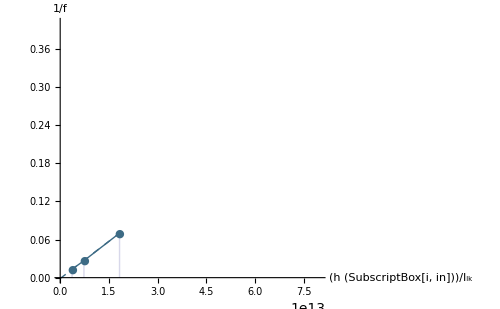
Current Fit Equation:  3.89768×10^-15 t-0.00135689
-Graphics-
ρ_tau:  3.89768×10^-15
Theoretical τ values:  {0.001,0.002,0.005}
Equivalent τ values:  {0.00117154,0.00234307,0.00585768}

```mathematica
bifiIn=0.6;
bifMaxX=8*10^13;
bifMaxY=0.4;
bifIndex=Position[iInVals,bifiIn]⟦1,1⟧;
plotVals⟦bifIndex⟧⟦1;;3⟧;
bifTauFitEq=Fit[plotVals⟦bifIndex⟧⟦1;;3⟧,{1,t},t];
bifTauFitRules=FindFit[plotVals⟦bifIndex⟧⟦1;;3⟧,m t+b,{m,b},t];
bifEquivalentTauVals=m/IlkValues⟦1;;3⟧/.bifTauFitRules;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[bifTauFitEq,Italic]}]},
{Show[
ListLinePlot[plotVals⟦bifIndex⟧⟦1;;3⟧,PlotRange->{{0,bifMaxX},{0,bifMaxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦1⟧,ImageSize->imageSize],
ListPlot[plotVals⟦bifIndex⟧⟦1;;3⟧,PlotStyle->dataStyle⟦1⟧,ImageSize->imageSize, Filling->Axis, PlotMarkers->{Automatic,Medium},PlotRange->{{0,bifMaxX},{0,bifMaxY}}],
Plot[bifTauFitEq,{t,0,2*10^13},PlotStyle->dashedStyle⟦1⟧,ImageSize->imageSize]
]},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.bifTauFitRules,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauVals⟦1;;3⟧,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[bifEquivalentTauVals,Italic]}]}
}]
```

## Appendix

### Color Chooser

Vary the index value of ColorData and see new colors appear.  These values once set change the colors used in the plot.

```mathematica
dataStyle=Reverse[Join[ColorData[90,"ColorList"],ColorData[31,"ColorList"]]];
dashedStyle=Tuples[{{Dashed}, dataStyle}];
boldStyle=Tuples[{{Thick}, dataStyle}];
Graphics[{#,PointSize[1],Point[{0,0}]},ImageSize-> 30]&/@dataStyle
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Input and Organize data

```mathematica
(*tauFiringRatesRawData=({{f, 5, 15, 25, 55}, {.001, 472.31, 820.09, 1039.2, 1470.5}, {.002, 241.17, 418.33, 527.77, 740.52}, {.005, 98.64, 171.29, 215.55, 300.49}, {.010, 49.81, 86.92, 109.4, 152.08}, {.015, 33.27, 58.27, 73.46, 102.17}, {.020, 24.92, 43.90, 55.33, 77.01}, {.025, 19.89, 35.19, 44.41, 61.88}});
iInValues=Rest[tauFiringRatesRawData⟦1⟧];
tauValues=Rest[Transpose[tauFiringRatesRawData]⟦1⟧];
Ilkbase=332.698*10^-15;
IlkValues={Ilkbase/0.1,Ilkbase/0.2,Ilkbase/0.5,Ilkbase/1.0,Ilkbase/1.5,Ilkbase/2.0,Ilkbase/2.5};
xValues=Transpose[h[#]&/@iInValues/#&/@IlkValues];
firingRatePlotVals=Transpose[1/Transpose[Rest[Transpose[Rest[tauFiringRatesRawData]]]]];
plotVals1=Transpose[{xValues⟦#⟧,firingRatePlotVals⟦#⟧}]&/@Range[Length[xValues]]
fitLineEq=Fit[#,{1,t},t]&/@plotVals1
fitLineRules=FindFit[#,m t+b,{m,b},t]&/@plotVals1*)
```